# Avaliação do Comportamento das Perdas de uma Linha de Transmissão Aérea

## Antonio C S Lima Agosto 2025

## Dados gerais

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Documents/Documents - oslo/Wolfram/00_EEE457

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Arial", 12},ImageSize-> 300,Joined-> True,
Axes-> False,Frame-> True,Joined-> True, AspectRatio-> 0.5];
```

```mathematica
SetOptions[{ Plot, LogPlot, LogLinearPlot, LogLogPlot},
BaseStyle->{FontFamily->"Arial", 16},ImageSize-> 600, 
Axes-> False,Frame-> True];
```

## Circuito de 138 kV

a partir dos dados do circuito 138CST1 do relatório da EPE, com o condutor DOVE

```mathematica
z1= 0.12201634999153511+0.48345448483576975  I;
y1=I 3.46770008354597  10^-6;
γ = Sqrt[z1 y1];
Zc= Sqrt[z1/y1];
Vn= 138 10^3;
Pn = Vn^2/Re[Zc];
```

função para o cálculo das perdas

```mathematica
calcPerdas[x_,z_, y_, pr_, vrff_,vb_, fp_:1, sng_:1]:= Module[{γ,zc,a,b,c,s,vr,ir, vs, is,pnom, perdas},
γ= Sqrt[ z y];
zc = Sqrt[z/y];
pnom = vb^2 /Re[zc];
a= Cosh[γ x];
b= zc Sinh[γ x];
c= 1/zc Sinh[γ x];
s = pr/fp;
ir=s Conjugate[Exp[sng I ArcCos[fp] ] ]/(Sqrt[3] vr);
vr= vb vrff/Sqrt[3];
 vs= a vr + b ir;
is = c vr + a ir;
perdas = (Re[vs Conjugate[is] - vr Conjugate[ir]]);
If[ .95<=Abs@#1  Sqrt[3]/vrff <=1.1, 
Return[3 *perdas], Nothing]&/@Abs[vs]
]
```

```mathematica
Pn
```

1.33163×10^8

```mathematica
calcPerdas[50.,z1, y1,  Pn, 1.0, Vn,.9, -1]/Pn
```

0.000971346

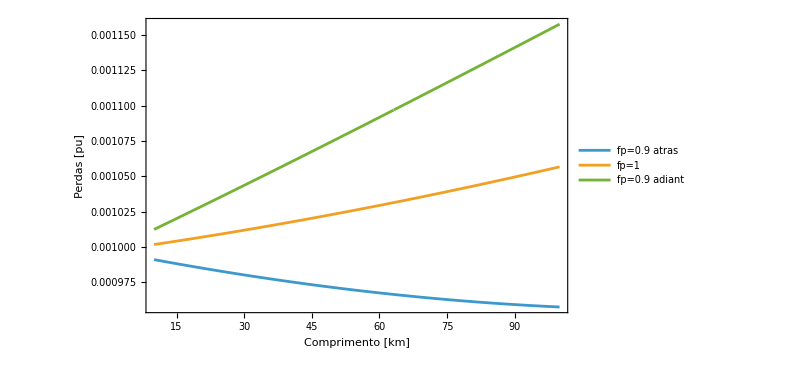

```mathematica
g1=Plot[{
calcPerdas[x,z1, y1,  Pn, 1.0, Vn,.9, -1]/Pn,
calcPerdas[x, z1, y1,  Pn, 1.0, Vn,1.,  1]/Pn,
calcPerdas[x, z1, y1,  Pn, 1.0, Vn,.9,  1]/Pn
},{x,10,100}, FrameLabel->{"Comprimento [km]", "Perdas [pu]"},
PlotLegends->Placed[LineLegend[{"fp=0.9 atras ","fp=1","fp=0.9 adiant"}],{.2,.85}]]
```

```mathematica
(*
g2=Plot[{
calcPerdas[x, Pn, .95Vn, .9, -1]/Pn,
calcPerdas[x, Pn, .95Vn ]/Pn,
calcPerdas[x, Pn, .95Vn, .9, 1]/Pn
},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Perdas [pu]"},
PlotLegends->Placed[LineLegend[{"fp=0.9 atras","fp=1","fp=0.9 adiant"}],{.2,.85}]];
g3=Plot[{
calcPerdas[x, Pn, 1.05Vn]/Pn,
calcPerdas[x, Pn, 1.05Vn, .9, 1]/Pn,
calcPerdas[x, Pn, 1.05Vn, .9, -1]/Pn
},{x, 50,300}, FrameLabel->{"Comprimento [km]", "Perdas [pu]"},
PlotLegends->Placed[LineLegend[{"fp=1","fp=0.9 atras","fp=0.9 adiant"}],{.2,.85}]];

GraphicsRow[{g1, g2, g3}, ImageSize->1800]
*)
```

## Circuito de 230 kV

a partir dos dados do circuito 138CSH1 do relatório da EPE, com o condutor GROSSBEAK

```mathematica
z1= 0.1020 + I.5094;
y1=I 3.2599  10^-6;
γ = Sqrt[z1 y1];
Zc= Sqrt[z1/y1];
Vn= 230 10^3;
Pn = Vn^2/Re[Zc];
```

função para o cálculo das perdas